```mathematica
(* specify directory containing image and its segmentation and cellular Voronoi diagram .json file if available; make this the working directory *)
(* workingDirectory=NotebookDirectory[]<>"Mmp2 RNAi gut/" *)
workingDirectory=NotebookDirectory[]
SetDirectory[workingDirectory];
```

/Users/james/Desktop/New New Aspect Ratio/

```mathematica
(* Find the filenames of the image and segmentation *)
imageFilename=FileNames["*.tif"][[1]]
segmentFilename = FileNames["Segments/*.tif"][[1]]
cvdFilename = "cellularVoronoiDiagramList.json"
```

Gut-0015 (1).zvi - C=0.tif

Segments/Segment_0_000.tif

cellularVoronoiDiagramList.json

```mathematica
(* Import the original image (cellImage) and the Segment image (segmentImage) *)
cellImage=Import[imageFilename];
{w,h} = ImageDimensions[cellImage];
segmentImage=Import[segmentFilename];

{wS,hS} = ImageDimensions[segmentImage];
If[w≠wS || h≠hS,
Print["WARNING! Image and Segmented Image have different dimensions!"],Print["OK. Image and Segmented Image have same dimensions: ",{w,h}]
]
GraphicsRow[{cellImage,ImageAdjust[segmentImage]}]
```

OK. Image and Segmented Image have same dimensions: {1388,1040}

-Graphics-

```mathematica
(* Get the list of cell IDs and exclude cells on the boundary of the image *)
pixelArray=ImageData[segmentImage,"Bit16"];
cellIDs=Sort[DeleteDuplicates[Flatten[pixelArray]]]
boundaryCellIDs=DeleteDuplicates[Join[pixelArray[[All,1]],pixelArray[[All,-1]],pixelArray[[1]],pixelArray[[-1]]]]
includedCellList=Complement[cellIDs,boundaryCellIDs]
Ncells=Length[includedCellList]
```

{1,3,4,5,6,7,8}

{1}

{3,4,5,6,7,8}

6

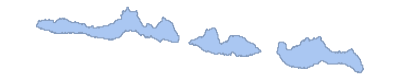

-Graphics-

```mathematica
(* Get a list of cell regions and overlay on original image to double check segmentation *)
cellRegionList=Table[ImageMesh[Binarize[segmentImage,{ci,ci+0.1}/(2^16 -1)],Method->"Exact"],{ci,includedCellList}];
allCellsRegion=ImageMesh[Binarize[segmentImage,1/(2^16 -1)],Method->"Exact"]
Show[
cellImage,
Graphics[{
Table[
{Directive[{ColorData["RedBlueTones",RandomInteger[Ncells]/Ncells],Opacity[0.5]}],MeshPrimitives[cellRegion,2]},
{cellRegion,cellRegionList}],
White, Opacity[0.5],MeshPrimitives[allCellsRegion,2]}
],ImageSize->Large
]
```

```mathematica
(* Calculate various attributes for all cells *)
centroidList=Table[ RegionCentroid[cellRegion],{cellRegion,cellRegionList}];
areaList=Table[ Area[cellRegion],{cellRegion,cellRegionList}];
perimeterList=Table[ Perimeter[cellRegion],{cellRegion,cellRegionList}];
shapeIndexList=Table[ perimeterList[[i]]/Sqrt[areaList[[i]]],{i,Ncells}];
(* several functions that go from moment of inertia (J) tensor to cell aspect ratio (kappa) and elongation direction (alpha) *)
jTensorList=Table[ MomentOfInertia[cellRegion],{cellRegion,cellRegionList}];
jEigenList=Eigensystem/@jTensorList;
kappaList=Sqrt[#[[1,1]]/#[[1,2]]]&/@jEigenList;
alphaList=ArcTan[#[[2,2]],#[[2,1]]][[1]]&/@jEigenList;
```

-106.02+4.54093 x-0.0102868 x^2+9.94026×10^-6 x^3-3.53321×10^-9 x^4

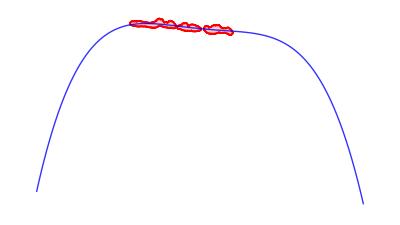

```mathematica
(* Will need a way to estimate the local tangent to the gut, i.e., the allCellsRegion *)
(* This region has a variety of thicknesses and is not continuous *)
allCellsPixelList=ImageValuePositions[Binarize[segmentImage,1/(2^16 -1)],1];
gutline=Fit[allCellsPixelList,{1,x,x^2,x^3,x^4},x]
Graphics[{Red,Point[#]&/@allCellsPixelList, White,Opacity[0.8],MeshPrimitives[allCellsRegion,2],Blue,Line[Table[{x,gutline},{x,1,w}]]}]
```

1

{-0.113887,-0.0724582,-0.112391,-0.0689568,0.115505,0.0375181}

{180.436,179.864,182.67,-164.533,162.474,169.388}

{0.436278,179.864,2.67005,15.4671,162.474,169.388}

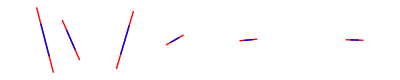

```mathematica
(* find the slope of the gutline at each cell's centroid and see if the cell's elongation is along or normal to the gutline *)
ci = RandomInteger[{1,Ncells}]
gutlineTangentAngleList=Table[ArcTan[D[gutline,x]/.x->centroidList[[ci,1]]],{ci,Ncells}]
(* use ArcCos[Cos[θ]] to convert all angles to range 0 to 180 degrees *)
alphaRelDegreeList=(alphaList-gutlineTangentAngleList)/Degree
alphaRelDegreeList2=Mod[#,180]&/@alphaRelDegreeList
Graphics[{Red,Table[Line[{{centroidList[[i,1]],0}+10{Cos[alphaRelDegreeList[[i]]Degree],Sin[alphaRelDegreeList[[i]]Degree]},{centroidList[[i,1]],0}-10{Cos[alphaRelDegreeList[[i]]Degree],Sin[alphaRelDegreeList[[i]]Degree]}}],{i,Ncells}],Blue,
Table[Line[{{centroidList[[i,1]],0}+5{Cos[alphaRelDegreeList2[[i]]Degree],Sin[alphaRelDegreeList2[[i]]Degree]},{centroidList[[i,1]],0}-5{Cos[alphaRelDegreeList2[[i]]Degree],Sin[alphaRelDegreeList2[[i]]Degree]}}],{i,Ncells}]
}]
```

4.77337

{{{0,0},{0.0076145,4.50045}},{{0,0},{3.13921,4.77337}},{{0,0},{0.0466011,2.54997}},{{0,0},{0.269952,3.65637}},{{0,0},{2.8357,3.23975}},{{0,0},{2.95638,3.66513}}}

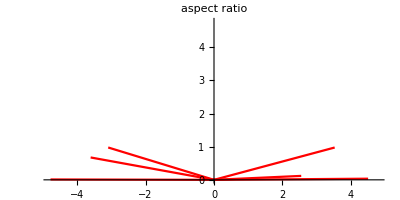

```mathematica
maxKappa=Max[kappaList]
dataForPolarPlot=Table[{{0,0},{alphaRelDegreeList2[[i]] Degree,kappaList[[i]]}},{i,Ncells}]
ListPolarPlot[dataForPolarPlot, Joined->True,PlotStyle->Red,PolarGridLines->None,PlotRange->{{-maxKappa,maxKappa},{0,maxKappa}},AxesLabel->"aspect ratio"]
```

```mathematica
(* Make an image that shows results for cell area and elongation; no designation of domains or wound location yet *)
propertyList=Sin/@(alphaRelDegreeList2 Degree) (* cell area, but can change this if you want to color-code by a different property *) 

overlayOnImage=True;
showElongationDirections=True;
s = 6; (* scale factor for aspect ratio lines that show elongation direction *)

minValue = Min[propertyList];
minValue=0
maxValue = Max[propertyList];
maxValue=1
coloring = "RedBlueTones";

Show[
ImageAssemble[{
If[overlayOnImage,cellImage,Graphics[{White,Polygon[{{0,0},{0,w},{h,w},{h,0}}]},ImageSize->{w,h}]],Rasterize[Rotate[ColorData[coloring,"Image"],π/2],RasterSize->{120,h}]}],
Graphics[
Table[
{
Directive[{ColorData["RedBlueTones",(propertyList[[i]]-minValue)/(maxValue-minValue)],
Opacity[If[overlayOnImage,0.5,1]]}],
MeshPrimitives[cellRegionList[[i]],2],
White,
Line[{centroidList[[i]]+s(kappaList[[i]]-1){Cos[alphaList[[i]]],Sin[alphaList[[i]]]},centroidList[[i]]-s (kappaList[[i]]-1){Cos[alphaList[[i]]],Sin[alphaList[[i]]]}}]
},
{i,Length[cellRegionList]}]
],
Graphics[{White,
Text[Style[ToString[Round[minValue,0.01]],FontSize->12],{w+60,10}],Text[Style[ToString[Round[maxValue,0.01]],FontSize->12],{w+60,h-10}],
Black,
Text[Style["Sin[α]",FontSize->14],{w+20,h/2},{0,0},{0,1}]}]
,ImageSize->Large
]
```

{0.00761442,0.0023796,0.0465842,0.266686,0.301143,0.184157}

0

1

-Graphics-

```mathematica
(* define functions for converting between Index and Image coordinates *)
ConvertToIndexCoord[pt_]:=({h-y+1/2,x+1/2})/.{x-> pt[[1]],y-> pt[[2]]}
ConvertToImageCoord[pt_]:=({c-1/2, h-r+1/2})/.{r-> pt[[1]],c-> pt[[2]]}
```

6

(4613.71 | 6578.39
6578.39 | 47850.8)

2.9939

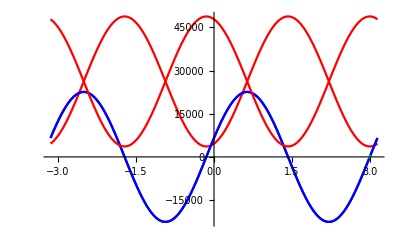

```mathematica
(* Checks on syntax for correctly rotating tensors in Mathematica *)
ci=RandomInteger[{1,Ncells}]
j=jTensorList[[ci]];
(* j={{2,0},{0,1}}.RotationMatrix[π/6] *)
MatrixForm[j]
jRot11=Table[{θ,(RotationMatrix[-θ].j.RotationMatrix[θ])[[1,1]]},{θ,-π,π,π/100}];
jRot12=Table[{θ,(RotationMatrix[-θ].j.RotationMatrix[θ])[[1,2]]},{θ,-π,π,π/100}];
jRot21=Table[{θ,(RotationMatrix[-θ].j.RotationMatrix[θ])[[2,1]]},{θ,-π,π,π/100}];
jRot22=Table[{θ,(RotationMatrix[-θ].j.RotationMatrix[θ])[[2,2]]},{θ,-π,π,π/100}];


alphaList[[ci]]
ListPlot[{jRot11,jRot12,jRot21,jRot22,{{alphaList[[ci]],0}}},PlotStyle->{Red,Blue,Blue,Red,Green},Joined->{True,True,True,True,False}]
```

```mathematica
(* Convert kappa and alphaRel to a single height/width w.r.t. gut axis aspect ratio as Angela did in her earlier studies *)
(* do a parallel transformation w.r.t. each cell's principal axis as a check on methods *)
jTensorRotatedPrincipalAxisList=Table[RotationMatrix[-alphaList[[i]]].jTensorList[[i]].RotationMatrix[alphaList[[i]]],{i,Ncells}];
jTensorRotatedGutAxisList=Table[RotationMatrix[-gutlineTangentAngleList[[i]]].jTensorList[[i]].RotationMatrix[gutlineTangentAngleList[[i]]],{i,Ncells}];

kappaRelPrincipalAxisList=Sqrt[#[[2,2]]/#[[1,1]]]&/@jTensorRotatedPrincipalAxisList;
(* note that Angela's reported aspect ratios for control cells, which are elongated along the gut axis, were <1 because of the way it was defined as heigh/width; hense dividing #[[1,1]]/#[[2,2]] below  *)
kappaRelGutAxisList=Sqrt[#[[1,1]]/#[[2,2]]]&/@jTensorRotatedGutAxisList;

TableForm[Transpose[{kappaList,alphaRelDegreeList2,kappaRelPrincipalAxisList,kappaRelGutAxisList}]]
```

4.50045 | 0.436278 | 4.50045 | 0.22233
4.77337 | 179.864 | 4.77337 | 0.209509
2.54997 | 2.67005 | 2.54997 | 0.394859
3.65637 | 15.4671 | 3.65637 | 0.387949
3.23975 | 162.474 | 3.23975 | 0.439511
3.66513 | 169.388 | 3.66513 | 0.330547

0.359248

0.0955667

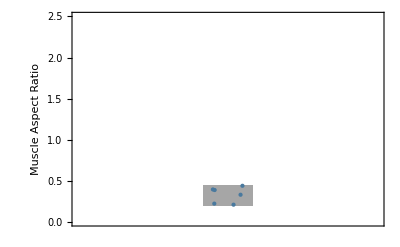

```mathematica
ClearAll[cef]
cef={ChartElementData["BoxWhisker"][##],EdgeForm[],FaceForm[None],ChartElementData["PointDensity","PointStyle"->Directive[EdgeForm[Black],PointSize[Large],Darker[Charting`ChartStyleInformation["Color"]]]][##]}&;
Median[kappaRelGutAxisList]
StandardDeviation[kappaRelGutAxisList]
BoxWhiskerChart[{kappaRelGutAxisList},PlotRange->{0,2.5},Frame->{{True,False},{False,False}},FrameLabel->{{"Muscle Aspect Ratio",None},{None,None}},ChartStyle->"Pastel",ChartElementFunction->cef]
```